### Notebook for power spectrum polynomial fitting

```mathematica
SetDirectory[NotebookDirectory[]]
```

#### Load linear spectrum

```mathematica
pofk=ReadList["pofk_z0.dat",{Number, Number}];
```

```mathematica
pl=Interpolation[Table[{pofk[[i,1]],pofk[[i,2]]},{i,1,Length[pofk]}]];
```

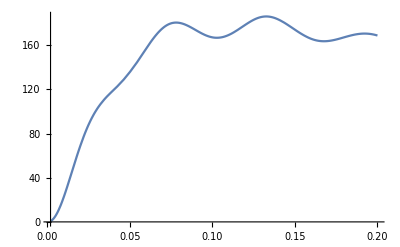

```mathematica
Plot[k^(3/2)*pl[k],{k,0.002,0.2}]
```

```mathematica
ytab=Table[pofk[[i,1]]^(3/2)*pofk[[i,2]],{i,1,Length[pofk]}];
xtab=Table[pofk[[i,1]],{i,1,Length[pofk]}];
pofktab=Transpose[{xtab,ytab}];
hlini[a1_,a2_,k_]:=a1+a2*k;
hlin[a1_,a2_]:=Table[a1+a2*pofk[[i,1]],{i,1,Length[pofk]}];
hlintab[a1_,a2_]:=Transpose[{xtab,hlin[a1,a2]}]
```

```mathematica
plini[a1_,a2_,a3_,a4_,a5_,a6_,a7_,k_]:=a1+a2*k+a3*k^2+a4*k^3+a5*k^4+a6*k^5+a7*k^6;
plin[a1_,a2_,a3_,a4_,a5_,a6_,a7_]:=Table[a1+a2*pofk[[i,1]]+a3*pofk[[i,1]]^2+a4*pofk[[i,1]]^3+a5*pofk[[i,1]]^4+a6*pofk[[i,1]]^5+a7*pofk[[i,1]]^6,{i,1,Length[pofk]}];
plintab[a1_,a2_,a3_,a4_,a5_,a6_,a7_]:=Transpose[{xtab,plin[a1,a2,a3,a4,a5,a6,a7]}]
```

```mathematica
pvlini[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_,a11_,a12_,k_]:=a1+a2*k+a3*k^2+a4*k^3+a5*k^4+a6*k^5+a7*k^6+a8*k^7+a9*k^8+a10*k^9+a11*k^10+a12*k^11;
pvlin[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_,a11_,a12_]:=Table[a1+a2*pofk[[i,1]]+a3*pofk[[i,1]]^2+a4*pofk[[i,1]]^3+a5*pofk[[i,1]]^4+a6*pofk[[i,1]]^5+a7*pofk[[i,1]]^6+a8*pofk[[i,1]]^(1/2)+a9*pofk[[i,1]]^(3/2)+a10*pofk[[i,1]]^(5/2)+a11*pofk[[i,1]]^(7/2)+a12*pofk[[i,1]]^(9/2),{i,1,Length[pofk]}];
pvlintab[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_,a11_,a12_]:=Transpose[{xtab,pvlin[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12]}]
```

```mathematica
Cost[a1_,a2_]:=Total[(hlin[a1,a2]-ytab)^2]
Costp[a1_,a2_,a3_,a4_,a5_,a6_,a7_]:=Total[(plin[a1,a2,a3,a4,a5,a6,a7]-ytab)^2]
Costpv[a1_,a2_,a3_,a4_,a5_,a6_,a7_,a8_,a9_,a10_,a11_,a12_]:=Total[(pvlin[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12]-ytab)^2]
```

```mathematica
Minimize[Cost[a1,a2],{a1,a2}]
Minimize[Costp[a1,a2,a3,a4,a5,a6,a7],{a1,a2,a3,a4,a5,a6,a7}]
Minimize[Costpv[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12],{a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12}]
```

{291119.,{a1→53.9727,a2→660.529}}

{4059.24,{a1→-18.6976,a2→4981.9,a3→-39322.1,a4→44146.2,a5→805868.,a6→-3.73129×10^6,a7→4.87305×10^6}}

{2923.08,{a1→-390.617,a2→-929766.,a3→-1.45977×10^8,a4→-3.68324×10^9,a5→-1.75522×10^10,a6→-9.61734×10^9,a7→1.55609×10^9,a8→30285.,a9→1.51013×10^7,a10→9.02236×10^8,a11→9.98313×10^9,a12→1.86325×10^10}}

```mathematica
"Mathematica's fitting isn't fantastic ..."
```

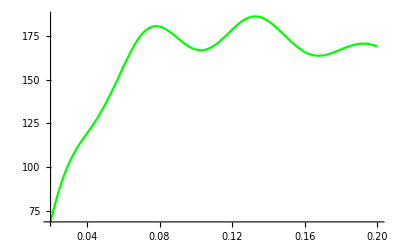

For illustration ....

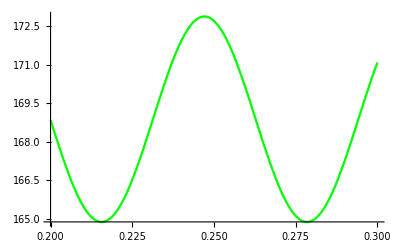

```mathematica
A=ListPlot[pofktab];
B=Plot[hlini[42,934,k],{k,0.01,0.2},PlotStyle->{Red}];
BB=Plot[plini[-19,5105,-45393,158350,-157851,-92157,-30812,k],{k,0.02,0.2},PlotStyle->{Orange}];
BBB=Plot[{pl[k]*k^(3/2)},{k,0.02,0.2},PlotStyle->{Green}]
"For illustration ...." 
BBBB=Plot[4Sin[100*k+2]+168.88,{k,0.2,0.3},PlotStyle->{Green}]
```

```mathematica
pl[0.2]*0.2^(3/2)
```

168.883

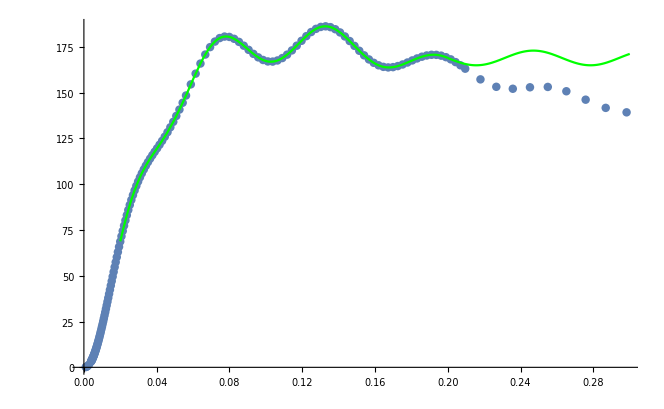

```mathematica
Show[A,BBB,BBBB]
```